```mathematica
Sptube[r_,θmin_,θmax_,dθ_,radius_]:=
Module[{a,θ},
a=Ball[{r Cos[-θmin],r Sin[-θmin],-θmin},radius];
For[θ=θmin+dθ,θ<θmax,θ+=dθ,
a=RegionUnion[a,Ball[{r Cos[θ],r Sin[θ],θ},radius]];
];
a]
```

```mathematica
radius=1/4;r=1;θmin=-π;θmax=π;
Ω=RegionUnion[Sptube[r,θmin,θmax,0.01,radius],Cylinder[{{r Cos[θmax],r Sin[θmax],θmax-0.05},{r Cos[θmax],r Sin[θmax],θmax+0.5}},radius],Cylinder[{{r Cos[θmin],r Sin[θmin],θmin+0.05},{r Cos[θmin],r Sin[θmin],θmin-0.5}},radius]];
```

```mathematica
Needs["NDSolve`FEM`"]
mesh=ToElementMesh[Ω,MaxCellMeasure->0.1]
```

ElementMesh[{{-1.2126,1.22772},{-1.23234,1.23243},{-3.64159,3.64159}},{TetrahedronElement[<3650>]}]

```mathematica
mr=MeshRegion[MeshOrderAlteration[mesh,1]];
hmr=HighlightMesh[RegionBoundary[mr],Sequence[Style[{2,All},Opacity[0.25]],ViewPoint->{2,0.6,0.9},ViewVertical->{-0.8,-0.18,0.5}]]
```

```mathematica
velocities = {u[t, x, y, z], v[t, x, y, z], w[t, x, y, z]};
op = {ρ*
Derivative[1,0,0,0][u][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][u[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][u[t, x, y, z], {x, y, z}] + 
Derivative[0,1,0,0][p][t, x, y, z], 
    ρ*
Derivative[1,0,0,0][v][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][v[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][v[t, x, y, z], {x, y, z}] + 
Derivative[0,0,1,0][p][t, x, y, z],
    ρ*
Derivative[1,0,0,0][w][t, x, y, z] + 
     Inactive[
       Div][(-μ Inactive[Grad][w[t, x, y, z], {x, y, z}]), {x, y, 
       z}] + ρ *
      velocities.Inactive[Grad][w[t, x, y, z], {x, y, z}] + 
Derivative[0,0,0,1][p][t, x, y, z], 
    
Derivative[0,1,0,0][u][t, x, y, z] + 
Derivative[0,0,1,0][v][t, x, y, z] + 
     D[w[t, x, y, z], z]} /. {μ -> 10^-3, ρ -> 1};
```

```mathematica
ramp=Function[t,Exp[5*t]/(Exp[20]+Exp[5*t])];
```

```mathematica
flowProfile[x_,y_]:=-((x-r Cos[θmax])^2/radius^2+(y-r Sin[θmax])^2/radius^2)+1
Plot3D[flowProfile[x,y],{x,y}∈Disk[{r Cos[θmax],r Sin[θmax]},radius]]
```

```mathematica
velocity=3/4;
inflowBC=DirichletCondition[{u[t,x,y,z]==0,v[t,x,y,z]==0,p[t,x,y,z]==0},z==θmax+0.5];
```

```mathematica
outflowBC=DirichletCondition[{u[t,x,y,z]==0,v[t,x,y,z]==0,p[t,x,y,z]==0},z==θmin-0.5];
```

```mathematica
wallBC=DirichletCondition[{u[t,x,y,z]==0,v[t,x,y,z]==0,w[t,x,y,z]==0},z≠θmax+0.5&&z≠θmin-0.5];
```

```mathematica
bcs={inflowBC,outflowBC,wallBC};
```

```mathematica
center1=RegionCentroid[Cylinder[{{r Cos[θmax],r Sin[θmax],θmax-0.05},{r Cos[θmax],r Sin[θmax],θmax+0.5}},radius]];
center2=RegionCentroid[Cylinder[{{r Cos[θmin],r Sin[θmin],θmin+0.05},{r Cos[θmin],r Sin[θmin],θmin-0.5}},radius]];
σ=0.001;
pf=Piecewise[{{PDF[MultinormalDistribution[center1,{{σ, 0,0},{0,σ,0},{0,0,σ}}],{x,y,z}],{x,y,z}∈Cylinder[{{r Cos[θmax],r Sin[θmax],θmax-0.05},{r Cos[θmax],r Sin[θmax],θmax+0.5}},radius]},{-PDF[MultinormalDistribution[center2,{{σ, 0,0},{0,σ,0},{0,0,σ}}],{x,y,z}],{x,y,z}∈Cylinder[{{r Cos[θmin],r Sin[θmin],θmin+0.05},{r Cos[θmin],r Sin[θmin],θmin-0.5}},radius]},{0,{x,y,z}∉Cylinder[{{r Cos[θmax],r Sin[θmax],θmax-0.05},{r Cos[θmax],r Sin[θmax],θmax+0.5}},radius]∧{x,y,z}∉Cylinder[{{r Cos[θmin],r Sin[θmin],θmin+0.05},{r Cos[θmin],r Sin[θmin],θmin-0.5}},radius]∧{x,y,z}∈Ω},{0,{x,y,z}∉Ω}}]/500;
Show[hmr,SliceContourPlot3D[pf,{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap"]],ImageSize->Medium]
Plot[pf/.{x->0,y->0},{z,-π,π}]
Plot[pf/.{x->0,z->center1[[3]]},{y,-radius,radius},PlotRange->All]
```

```mathematica
ic={u[0,x,y,z]==0,v[0,x,y,z]==0,w[0,x,y,z]==0,p[0,x,y,z]==pf};
```

```mathematica
n=0;
volume=NIntegrate[1,Element[{x,y,z},mesh]];
Monitor[AbsoluteTiming[{xVel,yVel,zVel,pressure}=NDSolveValue[{op=={0,0,0,0},bcs,ic},{u,v,w,p},{x,y,z}∈mesh,{t,0,5},Method->{"TimeIntegration"->{"IDA","MaxDifferenceOrder"->2},"PDEDiscretization"->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement","InterpolationOrder"->{u->2,v->2,w->2,p->1}}}},EvaluationMonitor:>(currentTime=Row[{"t = ",CForm[t]}])];],currentTime]
```

{15.5359,Null}

```mathematica
MaxMemoryUsed[]/1024.^2
```

1114.15

```mathematica
minmaxPressure=MinMax[pressure["ValuesOnGrid"]]
```

{-2.61263×10^-10,2.60533×10^-10}

```mathematica
Show[hmr,SliceContourPlot3D[pressure[0.000099999,x,y,z],{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap",Contours->Apply[Range,Flatten[{{-0.4,0.4},(-Apply[Subtract,{-0.4,0.4}])/10}]]]],ImageSize->Medium]
```

```mathematica
minmaxVel=MinMax[Flatten[{MinMax[xVel["ValuesOnGrid"]],MinMax[yVel["ValuesOnGrid"]],MinMax[zVel["ValuesOnGrid"]]}]]
```

{-1.60669×10^-16,1.59101×10^-16}

```mathematica
rmf=RegionMember[mr];
frames=Table[Show[hmr,VectorPlot3D[{xVel[t,x,y,z],yVel[t,x,y,z],zVel[t,x,y,z]},Evaluate[Sequence@@Join[{{x},{y},{z}},mesh["Bounds"]*1.01,2]],Sequence[VectorStyle->"Arrow3D",VectorColorFunction->"TemperatureMap",VectorScale->{Tiny,Scaled[0.4],None},VectorPoints->{10,10,10}],RegionFunction->(rmf[{#1,#2,#3}]&)],ImageSize->Medium],{t,0,5,1/6}];
```

```mathematica
rmf=RegionMember[mr];
frames=Table[Show[hmr,SliceContourPlot3D[pressure[0,x,y,z],{x,y,z}∈mesh,Sequence[ColorFunction->"TemperatureMap",Contours->Apply[Range,Flatten[{minmaxPressure,(-Apply[Subtract,minmaxPressure])/10}]]]],ImageSize->Medium],{t,0,20,1/6}];
```

```mathematica
ListAnimate[frames]
```

## pressure at (0 0 0):

```mathematica
center1
center2
```

{-1.,0.,3.36659}

{-1.,0.,-3.36659}

```mathematica
f=Table[pressure[x,-1.,0.,3.366592653589793],{x,0,5,0.001}];
g=Table[pressure[x,-1.,0.,-3.366592653589793],{x,0,5,0.001}];
ListPlot[{f,g}]
```

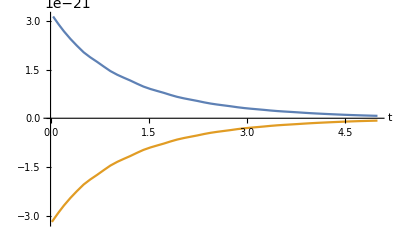

```mathematica
Plot[{pressure[t,-1.,0.,3.366592653589793],pressure[t,-1.,0.,-3.366592653589793]},{t,0,5},AxesLabel->Automatic]
```

```mathematica
0.
```

```mathematica
Plot[∫_(t+0)^(t+0.006) pressure[x,0.,0.,1.1]ⅆx,{t,0,0.01},PlotRange->All]
```

```mathematica
N[∫_0^1 pressure[x,0.,0.,1.1]ⅆx]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.000502969}. NIntegrate obtained 1.75342×10^-8 and 5.91649×10^-11 for the integral and error estimates.

1.75342×10^-8

```mathematica
NumberForm[1.7534238786220763*^-8,16]
```

1.753423878622076×10^-8

```mathematica
{t,center1}
```

{t,{0.,0.,1.225}}

```mathematica
Volume[Ω]
```

0.900018

```mathematica
Needs["NDSolve`FEM`"]
sregion=Disk[];
exact=Pi;
vars={x,y};
vd=NDSolve`VariableData[{"DependentVariables","Space"}->{{u},vars}];
sd=NDSolve`SolutionData["Space"->ToNumericalRegion[sregion]];
cdata=InitializePDECoefficients[vd,sd,"LoadCoefficients"->{{1}}];
mdata=InitializePDEMethodData[vd,sd];
ddata=DiscretizePDE[cdata,mdata,sd];
i1=Total[ddata["LoadVector"],2,Method->"CompensatedSummation"];
mesh=NDSolve`SolutionDataComponent[sd,"Space"]["ElementMesh"];
```

```mathematica
i3=NIntegrate[pf,Element[{x,y,z},mesh]]
```

0.000174206

```mathematica
n=0;
NDSolve[{y''[t]==-9.81,y[0]==0,y'[0]==0,WhenEvent[Mod[++n,2]===0,{y[t]->0,y'[t]->0}]},y,{t,0,10}];
Plot[y[t]/.%,{t,0,10}]
```

```mathematica
n=2;
Mod[++n,2]===0
```

False

```mathematica
,WhenEvent[Mod[++n,2]===0,pressure[t,x,y,z]->(1-NIntegrate[pressure[t,x,y,z],Element[{x,y,z},mesh]]/volume)*pressure[t,x,y,z]]
```

```mathematica
(1-NIntegrate[p[t,x,y,z],Element[{x,y,z},mesh]]/volume)*
```

```mathematica
Monitor[AbsoluteTiming[qsol=NDSolve[{y''[t]==-9.81,y[0]==0,y'[0]==0,WhenEvent[Mod[++n,2]===0,{y[t]->0,y'[t]->0}]},y,{t,0,0.5},EvaluationMonitor:>(currentTime=Row[{"t = ",CForm[t]}])];],currentTime]
Plot[y[t]/.qsol,{t,0,0.5}]
```

{15.1894,Null}